```mathematica
<<"../modules/importData.m"
```

Abundance vs. node degree:

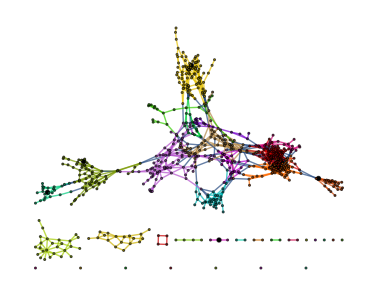
```mathematica
neutralNetwork=-Graphics-;
```

```mathematica
degree= VertexDegree[neutralNetwork]
```

{14,12,14,10,13,10,7,13,5,2,5,9,5,4,6,3,2,10,5,4,7,5,8,9,4,10,3,5,7,6,4,8,3,6,2,6,7,6,9,5,6,5,4,3,5,5,1,12,5,5,6,2,4,5,5,6,4,4,5,3,2,7,2,1,6,2,4,9,0,4,4,4,10,7,9,5,5,6,6,8,4,3,6,3,11,7,7,4,3,8,2,3,9,5,3,7,4,6,6,7,5,4,11,4,6,3,7,4,3,5,2,6,6,5,4,5,8,10,3,1,4,3,4,6,8,5,7,2,8,3,7,5,4,4,2,6,1,3,8,5,7,6,3,6,3,4,8,3,5,1,8,4,2,4,4,11,4,5,3,3,4,6,5,6,5,3,5,3,6,4,4,1,4,5,6,1,5,7,5,4,3,5,5,4,2,7,4,4,4,4,6,2,5,5,4,3,4,5,3,5,4,5,4,0,1,4,5,3,4,3,5,7,4,6,7,1,2,5,4,3,2,4,5,1,2,5,3,4,2,6,1,3,2,2,5,3,1,6,4,2,2,5,2,6,4,1,2,2,4,3,4,2,4,6,5,1,2,3,3,2,1,3,3,3,7,2,4,2,2,4,3,2,7,3,3,5,0,4,1,6,3,3,5,2,3,4,6,2,2,5,2,6,4,3,3,5,3,3,1,3,6,2,1,4,5,4,5,5,7,7,5,6,2,5,2,7,8,4,2,4,1,4,3,1,7,3,7,5,7,5,8,2,7,6,3,2,5,4,4,5,1,3,5,4,7,6,7,1,2,3,4,4,5,5,1,3,2,6,2,5,3,4,4,5,5,5,3,4,3,3,3,0,2,4,3,4,6,8,4,4,3,4,3,3,4,3,6,4,4,4,2,1,1,3,5,4,6,2,2,3,1,2,6,2,5,7,1,3,2,1,1,4,2,2,3,4,2,0,2,0,5,4,3,6,3,1,4,4,3,3,1,1,8,5,1,3,5,5,6,2,5,4,4,3,4,2,5,4,1,4,2,5,2,3,1,6,1,3,4,0,3,2,7,2,3,3,2,2,1,5,3,1,5,1,4,2,3,2,3,2,3,2,3,7,5,3,2,3,2,3,6,3,3,2,2,3,4,3,3,3,2,1,1,2,1,2,6,2,4,1,2,3,1,2,3,5,5,3,1,3,1,1,3,2,3,5,6,3,1,1,3,6,7,4,2,5,1,4,1,2,4,1,4,4,4,2,5,3,5,4,1,7,4,3,3,4,4,3,2,0,3,5,1,4,3,4,2,4,1,3,3,3,1,1,4,2,1,4,6,1,1,2,3,4,2,4,2,3,4,6,1,2,5,4,6,4,2,3,4,2,3,4,3,7,5,4,1,7,5,2,4,2,3,5,1,4,4,3,6,2,5,3,3,4,3,4,6,5,2,5,0,1,5,2,5,3,5,5,1,5,4,4,2,4,1,2,4,2,3,1,3,1,5,1,4,6,3,1,6,3,3,5,2,4,3,2,1,0,5,3,5,5,6,1,2,3,4,1,2,1,2,2,2,7,0,2,4,3,3,3,1,4,5,7,2,2,1,1,2,1,5,6,5,3,3,2,3,4,2,5,5,3,0,7}

```mathematica
abundance=importAbundanceTopol[];
```

```mathematica
x=degree;
y=abundance[[All,2]];
```

```mathematica
data=Transpose@{x,y};
```

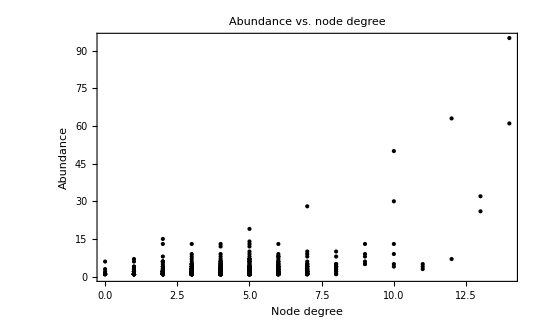

```mathematica
ListPlot[ data, PlotRange->All ,
PlotLabel->Style["Abundance vs. node degree", FontSize->18,FontFamily->"Arial", FontColor->Black],
PlotStyle->Black, Frame->True,
FrameLabel->Map[  Style[#,FontSize->18] &,{"Node degree","Abundance"}],
LabelStyle->Directive[Black]]
```

Spanish version:

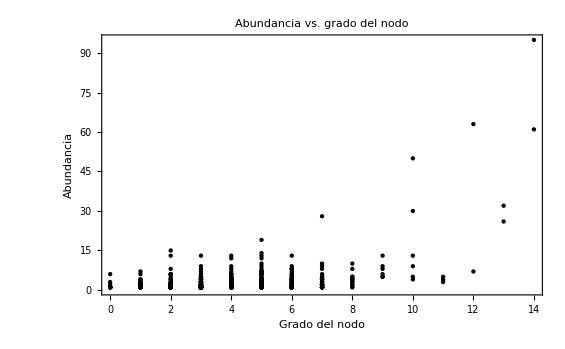

```mathematica
ListPlot[ data, PlotRange->All ,
PlotLabel->Style["Abundancia vs. grado del nodo", FontSize->18,FontFamily->"Arial", FontColor->Black],
PlotStyle->Black, Frame->True,
FrameLabel->Map[  Style[#,FontSize->18] &,{"Grado del nodo","Abundancia"}],
LabelStyle->Directive[Black]]
```

```mathematica
CorrelationTest[data,0,"TestDataTable"]
```

| Statistic | P-Value
Spearman Rank | 0.353752 | 6.2933×10^-23